```mathematica
Distance=2;
c=-2.20218;
Energy=4*c/Distance^2;
Λ[x_]=0.3127477*x-0.0231669*x^2-0.0005110 x^3-0.0000045 x^4;
```

```mathematica
λ[c]
```

λ[-2.20218]

```mathematica
(*angular equation*)
phiSol=NDSolve[{(1-η^2)D[f[η],{η,2}]-2η D[f[η],η]-(-Λ[c]+c η^2)f[η]==0,f[0.99999999]==1,f[-0.99999999]==1},f,{η,-0.99999999,0.99999999}]
```

{{f→InterpolatingFunction[…]}}

```mathematica
angSol[η_]=(f[η]/.phiSol)(1-η^2)^0
```

{InterpolatingFunction[…][η]}

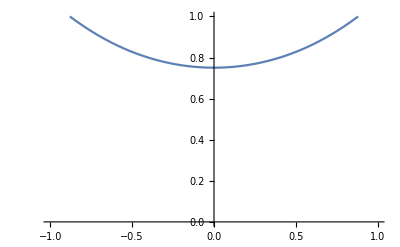

```mathematica
Plot[angSol[η],{η,-0.999,0.999},PlotRange->{0,1}]
```

```mathematica
NIntegrate[angSol[η]^2,{η,-0.999999,0.999999}]
```

{1.4831}

```mathematica
(*radial equation*)
(*biggest R possible*)
R=20
Rsol=NDSolve[{(ξ^2-1)D[g[ξ],{ξ,2}]+2ξ D[g[ξ],ξ]+(2*Distance* ξ +c ξ^2-Λ[c])g[ξ]==0,g[1.001]==1,g[R]==0},g,{ξ,1.000001,R}]
```

20

{{g→InterpolatingFunction[…]}}

{InterpolatingFunction[…][ξ]}

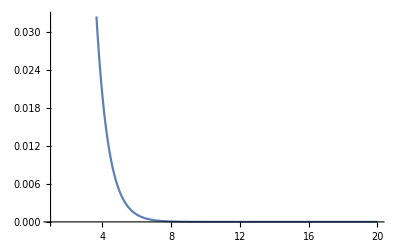

```mathematica
r[ξ_]=g[ξ]/.Rsol
Plot[r[ξ],{ξ,1.000001,R}]
```

```mathematica
NIntegrate[angSol[η]^2 r[ξ]^2 Distance^3/8(ξ^2-η^2),{ξ,1.001,10},{η,-0.999999,0.999999}]
```

{1.42132}

```mathematica
NIntegrate[r[ξ]^2,{ξ,1.001,10}]
```

{0.594659}

```mathematica
1.6169746217182044*0.9338651991415546
```

1.51004

```mathematica
ra[x_,z_]=√((z+Distance/2)^2+x^2);
rb[x_,z_]=√((z-Distance/2)^2+x^2);
ξ[x_,z_]=(ra[x,z]+rb[x,z])/Distance;
η[x_,z_]=(ra[x,z]-rb[x,z])/Distance;
```

```mathematica
x[2,2]
```

x[2,2]

```mathematica
NSolve[{ξ[x,z]==1,η[x, z]==0.5},{x}]
```

{}

```mathematica
ξ[x,z]
```

1/2 (√(x^2+(-1+z)^2)+√(x^2+(1+z)^2))

```mathematica
η[x, z]
```

1/2 (-√(x^2+(-1+z)^2)+√(x^2+(1+z)^2))

```mathematica
ψ[ξ_,η_]=r[ξ]*angSol[η]
```

{InterpolatingFunction[…][η] InterpolatingFunction[…][ξ]}

```mathematica
Ψ[x_,z_]=ψ[ξ[x,z],η[x,z]]
```

{InterpolatingFunction[…][1/2 (-√(x^2+(-1+z)^2)+√(x^2+(1+z)^2))] InterpolatingFunction[…][1/2 (√(x^2+(-1+z)^2)+√(x^2+(1+z)^2))]}

```mathematica
NIntegrate[ψ[ξ[x,z],η[x,z]],{x,0,5},{z,0,5}]
```

{2.515}

```mathematica
Ψ1[x_,z_]=Piecewise[{{ψ[ξ[x,z],η[x,z]],x>0 && z>0},{ψ[ξ[-x,z],η[-x,z]],x<=0 && z>0},{ψ[ξ[x,-z],η[x,-z]],x>0&&z≤0},{ ψ[ξ[-x,-z],η[-x,-z]],x≤0&&z≤0}}];
```

```mathematica
Ψ1[2.5,0]
```

{0.0931597}

```mathematica
Plot3D[Ψ1[x,z],{x,-5,5},{z,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
Ψ1[-1,0]
```

{0.534041}

```mathematica
Ψ1[0,0]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.936641}

```mathematica
NIntegrate[Ψ1[x,z]^2,{x,-5,5},{z,-5,5}]
```

NIntegrate::inum: Integrand ({ | «1»)^2 is not numerical at {x,z} = {2.5,-2.5}.

NIntegrate[Ψ1[x,z]^2,{x,-5,5},{z,-5,5}]

```mathematica
Ψ1[x,z]^2
```

(Piecewise[{{{InterpolatingFunction[…][1/2 (-√(x^2+(-1+z)^2)+√(x^2+(1+z)^2))] InterpolatingFunction[…][1/2 (√(x^2+(-1+z)^2)+√(x^2+(1+z)^2))]}, (x>0&&z>0)||(x≤0&&z>0)}, {{InterpolatingFunction[…][1/2 (-√(x^2+(-1-z)^2)+√(x^2+(1-z)^2))] InterpolatingFunction[…][1/2 (√(x^2+(-1-z)^2)+√(x^2+(1-z)^2))]}, (x>0&&z≤0)||(x≤0&&z≤0)}, {0, True}}])^2

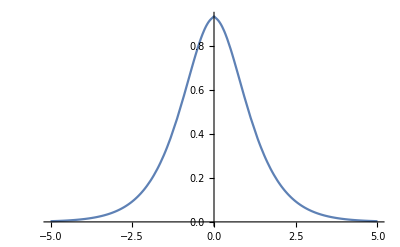

```mathematica
Plot[Ψ1[x,0],{x,-5,5}]
```

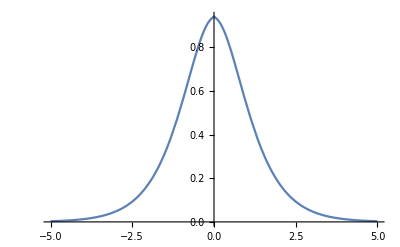

```mathematica
Plot[Ψ1[x,0.1],{x,-5,5}]
```

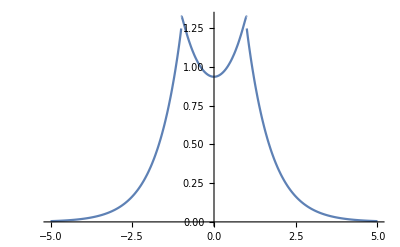

```mathematica
Plot[Ψ1[0,x],{x,-5,5}]
```

```mathematica
Ψ1[0,-1]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

Piecewise[{{True, {1.26215}}, {0, True}}]

```mathematica
ψ[1,0]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.936641}

```mathematica
angSol[0]
```

{0.733693}

```mathematica
NIntegrate[angSol[x]^2,{x,-0.999,0.999}]
```

{1.41458}